# Time Series, Sound, Audio and Image Data

# Murilo da Silva Baptista murilo.baptista@abdn.ac.uk

## Overview

This Lecture covers

Time Series

Temporal data

Sound and Images

# Time Series

A time series is a series of data points representing measurements of one or more variables conducted usually at a fixed location(s) and indexed (or listed or graphed) in time order.

Very often the measurements are conducted successive equally spaced points in time, so defining a sampling rate for the measurements: 1Hz meaning that 1 point is collected at each second.

Examples: Electroencephalogram (EEG), ocean tides, ocean surface temperature, the daily closing value of the Dow Jones Industrial Average...

[Wikipedia]  Motivation behind Time Series analysis:

To forecast: in the context of statistics, econometrics, quantitative finance, seismology, meteorology, and geophysics: forecasting.

Signal detection and estimation: in the context of signal processing, control engineering and communication.

Clustering, classification, query by content, anomaly detection as well as forecast: in the context of data mining, pattern recognition and machine learning time series analysis.

# Time Series in Wolfram

```mathematica
v={2,1,6,5,7,4};
t={1,2,5,10,12,15};
```

```mathematica
time=TimeSeries[v,{t}]
```

TimeSeries[…]

```mathematica
Clear[t]
```

```mathematica
{t,v}
```

```mathematica
{{1,2,5,10,12,15},{2,1,6,5,7,4}}//Transpose
```

{{1,2},{2,1},{5,6},{10,5},{12,7},{15,4}}

```mathematica
{t,v}//Transpose//MatrixForm
```

(1 | 2
2 | 1
5 | 6
10 | 5
12 | 7
15 | 4)

Or : Combine the two lists to get an Array to fit format TimeSeries {{t_ 1, v_ 1}, {t_ 2, v_ 2}, {t_i, v_i}}

```mathematica
Transpose[{t,v}]//MatrixForm
```

(1 | 2
2 | 1
5 | 6
10 | 5
12 | 7
15 | 4)

```mathematica
time2=TimeSeries[Transpose[{t,v}]]
```

TimeSeries[…]

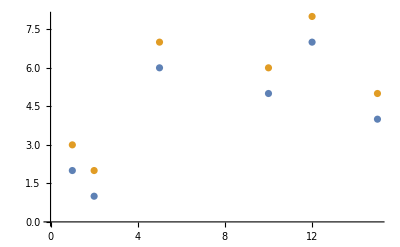

```mathematica
ListPlot[{time,time2+1}]
```

# Financial Data (timeseries)

```mathematica
FinancialData["GE","Properties"]
```

{AdjustedClose,AdjustedHigh,AdjustedLow,AdjustedOHLC,AdjustedOHLCV,AdjustedOpen,AdjustedRange,Ask,AskSize,Average200Day,Average50Day,AverageVolume3Month,Bid,BidSize,BookValuePerShare,Change,Change200Day,Change50Day,ChangeHigh52Week,ChangeLow52Week,CIK,Close,Company,CumulativeFractionalChange,CumulativeReturn,Dividend,DividendPerShare,DividendYield,EarningsPerShare,EarningsYield,EBITDA,Exchange,FloatShares,FractionalChange,FractionalChange200Day,FractionalChange50Day,FractionalChangeHigh52Week,FractionalChangeLow52Week,High,High52Week,IPODate,Last,LastTradeSize,LatestTrade,Lookup,Low,Low52Week,MarketCap,MIC,Name,OHLC,OHLCV,Open,PERatio,Price,PriceToBookRatio,PriceToSalesRatio,Range,Range52Week,RawClose,RawHigh,RawLow,RawOHLC,RawOHLCV,RawOpen,RawRange,RawVolume,Return,Sector,SICCode,StandardName,Symbol,Volatility20Day,Volatility250Day,Volatility50Day,Volume,Website}

```mathematica
DateListPlot[{FinancialData["GE","Price",{{2019,1,1},{2026,1,19}}],FinancialData["Amazon","Price",{{2019,1,1},{2026,1,19}}]},PlotLabels->{"GE","Amazon"},DateTicksFormat->{"MonthNameShort"," ","YearShort"},FrameLabel->{"Date",None}]
```

-Graphics-

## Cryptocurrency

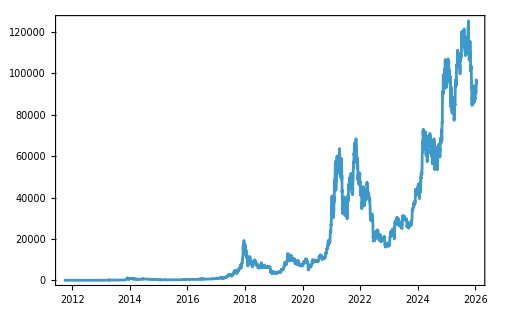

```mathematica
DateListPlot[FinancialData["BTC/USD",{{2009,3,1},{2026,1,19}}]]
```

## Temporal Data

For Multivariate timeseries !

In the previous example, we looked at a typical example of easily read data, but a structure that is basically incompatible with deep time-series analysis and also to multivariate data. 

Use the TemporalData function to make the data useful for your analysis, while leaving it in a form that is easy for humans to read.

```mathematica
path=NotebookDirectory[]
```

/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/

```mathematica
SetDirectory[path <> "DataDir/Lec5"]
```

/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec5

```mathematica
Directory[]
```

/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec5

```mathematica
?TemporalData
```

```mathematica
FileNames[]
```

{.DS_Store,stockhighlowclose.tsv,vix-daily_csv.csv}

```mathematica
stkDat22= Import["stockhighlowclose.tsv"];
```

```mathematica
stkDat22//TableForm
```

{{2006, 7, 3}, 11277.09} | {{2006, 7, 5}, 11239.47} | {{2006, 7, 6}, 11301.58} | {{2006, 7, 7}, 11227.62} | {{2006, 7, 10}, 11174.47} | {{2006, 7, 11}, 11186.32} | {{2006, 7, 12}, 11181.12} | {{2006, 7, 13}, 11015.19} | {{2006, 7, 14}, 10892.64} | {{2006, 7, 17}, 10858.22} | {{2006, 7, 18}, 10867.02} | {{2006, 7, 19}, 11038.16} | {{2006, 7, 20}, 11098.75} | {{2006, 7, 21}, 10995.73} | {{2006, 7, 24}, 11096.35} | {{2006, 7, 25}, 11133.73} | {{2006, 7, 26}, 11208.09} | {{2006, 7, 27}, 11245.47} | {{2006, 7, 28}, 11282.05} | {{2006, 7, 31}, 11265.8} | {{2006, 8, 1}, 11210.65} | {{2006, 8, 2}, 11228.98} | {{2006, 8, 3}, 11304.78} | {{2006, 8, 4}, 11367.94} | {{2006, 8, 7}, 11294.14} | {{2006, 8, 8}, 11319.51} | {{2006, 8, 9}, 11296.22} | {{2006, 8, 10}, 11176.47} | {{2006, 8, 11}, 11121.4} | {{2006, 8, 14}, 11242.83} | {{2006, 8, 15}, 11271.25} | {{2006, 8, 16}, 11373.78} | {{2006, 8, 17}, 11372.34} | {{2006, 8, 18}, 11437.66} | {{2006, 8, 21}, 11381.46} | {{2006, 8, 22}, 11426.13} | {{2006, 8, 23}, 11394.75} | {{2006, 8, 24}, 11386.59} | {{2006, 8, 25}, 11350.09} | {{2006, 8, 28}, 11411.24} | {{2006, 8, 29}, 11432.38} | {{2006, 8, 30}, 11452.95} | {{2006, 8, 31}, 11451.03} | {{2006, 9, 1}, 11476.4} | {{2006, 9, 5}, 11533.87} | {{2006, 9, 6}, 11469.27} | {{2006, 9, 7}, 11443.66} | {{2006, 9, 8}, 11448.3} | {{2006, 9, 11}, 11468.88} | {{2006, 9, 12}, 11512.74} | {{2006, 9, 13}, 11605.59} | {{2006, 9, 14}, 11548.84} | {{2006, 9, 15}, 11661.38} | {{2006, 9, 18}, 11588.22} | {{2006, 9, 19}, 11605.67} | {{2006, 9, 20}, 11680.19} | {{2006, 9, 21}, 11677.39} | {{2006, 9, 22}, 11588.62} | {{2006, 9, 25}, 11616.23} | {{2006, 9, 26}, 11723.74} | {{2006, 9, 27}, 11775.6} | {{2006, 9, 28}, 11775.36} | {{2006, 9, 29}, 11782.49}
{{2006, 7, 3}, 11146.06} | {{2006, 7, 5}, 11083.94} | {{2006, 7, 6}, 11117.16} | {{2006, 7, 7}, 11040.32} | {{2006, 7, 10}, 11090.1} | {{2006, 7, 11}, 10987.33} | {{2006, 7, 12}, 10973.37} | {{2006, 7, 13}, 10790.82} | {{2006, 7, 14}, 10664.43} | {{2006, 7, 17}, 10668.35} | {{2006, 7, 18}, 10658.35} | {{2006, 7, 19}, 10796.74} | {{2006, 7, 20}, 10884.47} | {{2006, 7, 21}, 10778.58} | {{2006, 7, 24}, 10868.7} | {{2006, 7, 25}, 11000.05} | {{2006, 7, 26}, 10987.41} | {{2006, 7, 27}, 11040.8} | {{2006, 7, 28}, 11102.11} | {{2006, 7, 31}, 11115.24} | {{2006, 8, 1}, 11035.92} | {{2006, 8, 2}, 11124.52} | {{2006, 8, 3}, 11101.55} | {{2006, 8, 4}, 11165.11} | {{2006, 8, 7}, 11143.02} | {{2006, 8, 8}, 11117.8} | {{2006, 8, 9}, 11044.64} | {{2006, 8, 10}, 10998.06} | {{2006, 8, 11}, 11042.88} | {{2006, 8, 14}, 11049.68} | {{2006, 8, 15}, 11098.03} | {{2006, 8, 16}, 11207.85} | {{2006, 8, 17}, 11298.54} | {{2006, 8, 18}, 11273.49} | {{2006, 8, 21}, 11322.31} | {{2006, 8, 22}, 11279.25} | {{2006, 8, 23}, 11238.67} | {{2006, 8, 24}, 11232.83} | {{2006, 8, 25}, 11218.66} | {{2006, 8, 28}, 11240.91} | {{2006, 8, 29}, 11255.88} | {{2006, 8, 30}, 11309.99} | {{2006, 8, 31}, 11326.8} | {{2006, 9, 1}, 11381.14} | {{2006, 9, 5}, 11385.95} | {{2006, 9, 6}, 11395.15} | {{2006, 9, 7}, 11273.89} | {{2006, 9, 8}, 11295.18} | {{2006, 9, 11}, 11295.9} | {{2006, 9, 12}, 11396.83} | {{2006, 9, 13}, 11423.73} | {{2006, 9, 14}, 11495.77} | {{2006, 9, 15}, 11504.57} | {{2006, 9, 18}, 11528.43} | {{2006, 9, 19}, 11450.3} | {{2006, 9, 20}, 11514.5} | {{2006, 9, 21}, 11471.76} | {{2006, 9, 22}, 11423.57} | {{2006, 9, 25}, 11486.} | {{2006, 9, 26}, 11517.54} | {{2006, 9, 27}, 11595.75} | {{2006, 9, 28}, 11625.92} | {{2006, 9, 29}, 11642.17}
{{2006, 7, 3}, 11228.02} | {{2006, 7, 5}, 11151.82} | {{2006, 7, 6}, 11225.3} | {{2006, 7, 7}, 11090.67} | {{2006, 7, 10}, 11103.55} | {{2006, 7, 11}, 11134.77} | {{2006, 7, 12}, 11013.18} | {{2006, 7, 13}, 10846.29} | {{2006, 7, 14}, 10739.35} | {{2006, 7, 17}, 10747.36} | {{2006, 7, 18}, 10799.23} | {{2006, 7, 19}, 11011.42} | {{2006, 7, 20}, 10928.1} | {{2006, 7, 21}, 10868.38} | {{2006, 7, 24}, 11051.05} | {{2006, 7, 25}, 11103.71} | {{2006, 7, 26}, 11102.51} | {{2006, 7, 27}, 11100.43} | {{2006, 7, 28}, 11219.7} | {{2006, 7, 31}, 11185.68} | {{2006, 8, 1}, 11125.73} | {{2006, 8, 2}, 11199.92} | {{2006, 8, 3}, 11242.59} | {{2006, 8, 4}, 11240.35} | {{2006, 8, 7}, 11219.38} | {{2006, 8, 8}, 11173.59} | {{2006, 8, 9}, 11076.18} | {{2006, 8, 10}, 11124.37} | {{2006, 8, 11}, 11088.02} | {{2006, 8, 14}, 11097.87} | {{2006, 8, 15}, 11230.26} | {{2006, 8, 16}, 11327.12} | {{2006, 8, 17}, 11334.96} | {{2006, 8, 18}, 11381.47} | {{2006, 8, 21}, 11345.04} | {{2006, 8, 22}, 11339.84} | {{2006, 8, 23}, 11297.9} | {{2006, 8, 24}, 11304.46} | {{2006, 8, 25}, 11284.05} | {{2006, 8, 28}, 11352.01} | {{2006, 8, 29}, 11369.94} | {{2006, 8, 30}, 11382.91} | {{2006, 8, 31}, 11381.15} | {{2006, 9, 1}, 11464.15} | {{2006, 9, 5}, 11469.28} | {{2006, 9, 6}, 11406.2} | {{2006, 9, 7}, 11331.44} | {{2006, 9, 8}, 11392.11} | {{2006, 9, 11}, 11396.84} | {{2006, 9, 12}, 11498.09} | {{2006, 9, 13}, 11543.32} | {{2006, 9, 14}, 11527.39} | {{2006, 9, 15}, 11560.77} | {{2006, 9, 18}, 11555.} | {{2006, 9, 19}, 11540.91} | {{2006, 9, 20}, 11613.19} | {{2006, 9, 21}, 11533.23} | {{2006, 9, 22}, 11508.1} | {{2006, 9, 25}, 11575.81} | {{2006, 9, 26}, 11669.39} | {{2006, 9, 27}, 11689.24} | {{2006, 9, 28}, 11718.45} | {{2006, 9, 29}, 11679.07}

```mathematica
stkDat22[[1;;3,1]]
```

{{{2006, 7, 3}, 11277.09},{{2006, 7, 3}, 11146.06},{{2006, 7, 3}, 11228.02}}

```mathematica
Dimensions[stkDat22]
```

{3,63}

See that date and value is a single element, difficult to extract information.

```mathematica
stkDat22[[1,1]]
```

{{2006, 7, 3}, 11277.09}

Use ToExpression to extract {{date}, value} as 2 elements

```mathematica
stkDat2= ToExpression[Import["stockhighlowclose.tsv"]];
```

This data consists of three “rows”, as can be seen using Dimensions.

```mathematica
Dimensions[stkDat2]
```

{3,63,2}

In stkDat22, there is a single element despite the {}

```mathematica
stkDat22[[2,1]]
```

{{2006, 7, 3}, 11146.06}

```mathematica
stkDat2[[2,1,1;;2]]
```

{{2006,7,3},11146.1}

```mathematica
stkDat2[[2,1,2]]
```

11146.1

{D1,D2,D3}:

D1: three "rows" each with a list with the date and the values of High, Low and Close

D2: 63 columns for each day of Stock Market

D3: dimension of the list containing the date and the value

Values of High, Low, Close for the day {2006, 7, 3}

```mathematica
stkDat2[[1;;3,1]]
```

{{{2006,7,3},11277.1},{{2006,7,3},11146.1},{{2006,7,3},11228.}}

The bellow extracts High, Low, Close values for first “column” (day 1, 2006, 7, 3).

```mathematica
Table[stkDat2[[i,1]],{i,3}]
```

{{{2006,7,3},11277.1},{{2006,7,3},11146.1},{{2006,7,3},11228.}}

Construct a TemporalData object for your stock data.

```mathematica
td1=TemporalData[stkDat2]
```

TemporalData[…]

```mathematica
td1["Properties"]
```

{Components,DateList,DatePath,DatePaths,Dates,FirstDates,FirstTimes,FirstValues,LastDates,LastTimes,LastValues,Part,Path,PathComponent,PathComponents,PathCount,PathDates,PathFunction,PathFunctions,PathLength,PathLengths,Paths,PathTimes,SliceData,SliceDistribution,TimeList,Times,TimeZone,ValueDimensions,ValueList,Values}

Find the values of each path (a continuous mapping, a function applied to the time giving the values) for a particular day.

```mathematica
"SliceData" is a Property of TemporalData to show a slice through all paths at a given time. Time can be specified in any of the formats Mathematica accepts:
```

```mathematica
td1["SliceData",{"2006/07/17"}]
```

{{10858.2},{10668.4},{10747.4}}

```mathematica
td1["SliceData",{"2006 Jul 17"}]
```

{{10858.2},{10668.4},{10747.4}}

```mathematica
td1["SliceData",{"Jul 17 2006"}]
```

{{10858.2},{10668.4},{10747.4}}

Get the number of observations. There will be 63 observations, but each observation measures 3 values

```mathematica
td1["PathLengths"]
```

{63,63,63}

We could just manipulate the dataset as it is, for example to plot the values :

```mathematica
DateListPlot[td1, PlotLabels->{"High","Min","Close"}]
```

-Graphics-

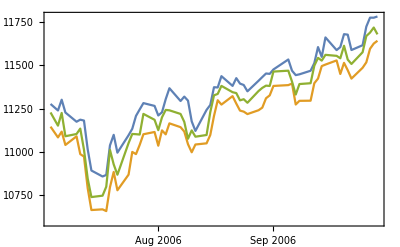

```mathematica
DateListPlot[td1]
```

DateListPlot was updated in Mathematica 12.

Mathematica allows general formats to plot the DateTicksFormat, for example:

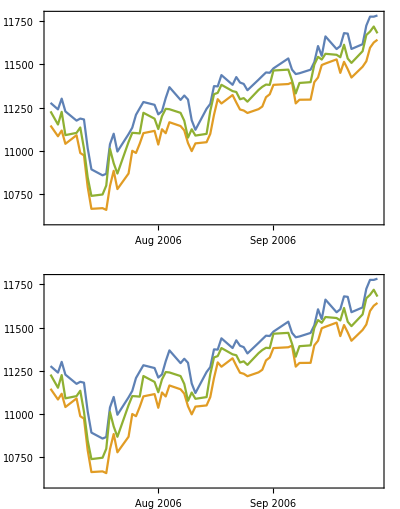

```mathematica
GraphicsGrid[{{DateListPlot[td1]},{DateListPlot[td1,DateTicksFormat->{"MonthShort","/","Day"}]}}]
```

```mathematica
(* -----*)
```

Just a local "appendix" : dates can also be specified by DateObject

```mathematica
data={{DateObject[{2016,10,1}],10},{DateObject[{2016,10,15}],17},{DateObject[{2016,10,30}],15},{DateObject[{2016,11,20}],20}}
```

{{Sat 1 Oct 2016,10},{Sat 15 Oct 2016,17},{Sun 30 Oct 2016,15},{Sun 20 Nov 2016,20}}

```mathematica
(* -----*)
```

In the following, we will do several manipulations to learn more about the way Mathematica deals with time (absolute time) and also how to deal with the data! This comes next.

# Transforming a Temporal data into a list and then to Table

## First steps to constructing a code in Wolfram

We want to put the data all together with the date with a single entry

Notice the list of elements for the day “1”:

```mathematica
Table[stkDat2[[i,1]],{i,3}]
```

{{{2006,7,3},11277.1},{{2006,7,3},11146.1},{{2006,7,3},11228.}}

Taking the last element of each sublist to get the values of High, Low and Close :

Using a Map function to apply the function Take. In this form, the function Take is applied 3 times, each time that the variable i assumes a different value

```mathematica
Map[Take[#,-1]&,Table[stkDat2[[i,1]],{i,3}]]
```

{{11277.1},{11146.1},{11228.}}

So, another way to extract the 3 values (High, Low, Close) for “day 1” would be to just do:

```mathematica
day=1
```

1

```mathematica
Table[stkDat2[[i,day,2]],{i,3}]
```

{11277.1,11146.1,11228.}

Flatten for a list of values, if the previous Map function option is used :

```mathematica
Flatten[Map[Take[#,-1]&,Table[stkDat2[[i,1]],{i,3}]]]
```

{11277.1,11146.1,11228.}

Prepend the date 1 to the list of Values, and transform the date in a list into a DateObject

```mathematica
Prepend[Flatten[Map[Take[#,-1]&,Table[stkDat2[[i,day]],{i,3}]]],DateObject[stkDat2[[1,day,1]]]]
```

{Mon 3 Jul 2006,11277.1,11146.1,11228.}

```mathematica
stkDat2[[1,day,1]]
```

{2006,7,3}

Prepend the date 2 to the list of Values

```mathematica
day=2;
```

```mathematica
Prepend[Flatten[Map[Take[#,-1]&,Table[stkDat2[[i,day]],{i,3}]]],DateObject[stkDat2[[1,day,1]]]]
```

{Wed 5 Jul 2006,11239.5,11083.9,11151.8}

```mathematica
stkDat2[[1,day,1]]
```

{2006,7,5}

Prepend the date 3 to the list of Values

```mathematica
day=3;
```

```mathematica
Prepend[Flatten[Map[Take[#,-1]&,Table[stkDat2[[i,day]],{i,3}]]],DateObject[stkDat2[[1,day,1]]]]
```

{Thu 6 Jul 2006,11301.6,11117.2,11225.3}

Now just create a rule in the form of a Table

```mathematica
tablevalues=Table[Prepend[Flatten[Map[Take[#,-1]&,Table[stkDat2[[i,day]],{i,3}]]],DateObject[stkDat2[[1,day,1]]]],{day,63}];
```

```mathematica
tablevalues;
```

Now, Prepend the "Keys"

```mathematica
tablevaluesWithKey=Prepend[tablevalues,{"Date","High","Low", "Close"}]//Dataset
```

## Absolute time

Times are returned as absolute times, and these are the times used in functions like ListPlot to locate points and ticks.

```mathematica
?AbsoluteTime
```

```mathematica
AbsoluteTime[]
```

3.977826715013011×10^9

```mathematica
td1
```

TemporalData[…]

```mathematica
td1["PathTimes"]//Short
```

{3360873600,3361046400,3361132800,3361219200,«55»,3368217600,3368304000,3368390400,3368476800}

First and last element of list

```mathematica
td1["PathTimes"][[{1,-1}]]
```

{3360873600,3368476800}

Use the FindDivisions function to determine where to place ticks.

```mathematica
1/5//N
```

0.2

```mathematica
FindDivisions[{0,1},6]//N
```

{0.,0.2,0.4,0.6,0.8,1.}

```mathematica
divs=FindDivisions[td1["PathTimes"][[{1,-1}]],5]
```

{3360000000,3362000000,3364000000,3366000000,3368000000,3370000000}

Combine the time locations with labels obtained from DateString.

The first date in DataString format is :

```mathematica
DateString[3360000000,{"MonthName"," ", "Year"," ", "Day"}]
```

June 2006 22

```mathematica
dateTcks=Transpose[{divs,DateString[#,{"MonthName"," ","Day"}]&/@divs}]
```

{{3360000000,June 22},{3362000000,July 16},{3364000000,August 08},{3366000000,August 31},{3368000000,September 23},{3370000000,October 16}}

Plot the three data sets for High, Low, Close:

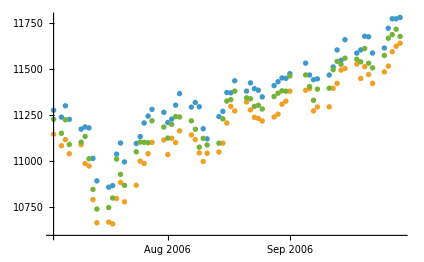

```mathematica
ListPlot[td1]
```

Automatic is for Y axis.

Join the points for the values of close

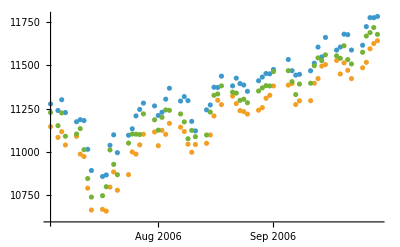

```mathematica
ListPlot[td1]
```

ListPlot deals well with time series, but if time series would have not been defined, the function would not know how to plot a dataset that has a column for string dates and values .

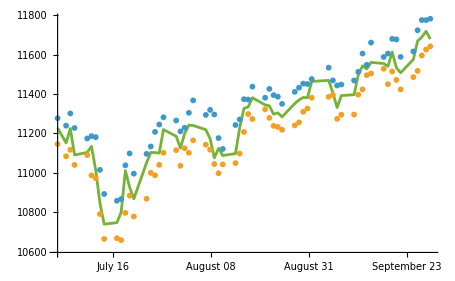

```mathematica
ListPlot[td1,Ticks-> {dateTcks,Automatic},Joined-> {False,False,True}]
```

Connect points from set 1 (High) to set 2 {Low}

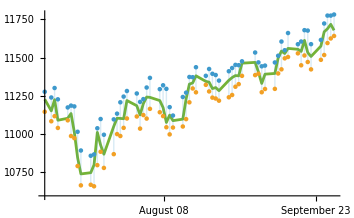

```mathematica
ListPlot[td1,Ticks-> {dateTcks,Automatic},Joined-> {False,False,True},Filling-> {1-> {2}}]
```

Of course in this example you could have used DateListPlot to obtain a similar visualization, but you would have missed the details of how Mathematica natively handles with time (e.g. absolute time), and also all this programming techniques to clean the data.

```mathematica
stkDat2;
```

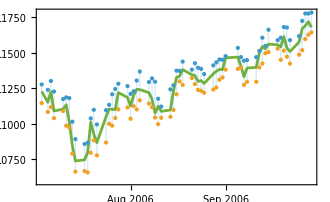

```mathematica
DateListPlot[stkDat2,Joined-> {False,False,True},Filling-> {1-> {2}}]
```

```mathematica
dateTcks
```

{{3360000000,June 22},{3362000000,July 16},{3364000000,August 08},{3366000000,August 31},{3368000000,September 23},{3370000000,October 16}}

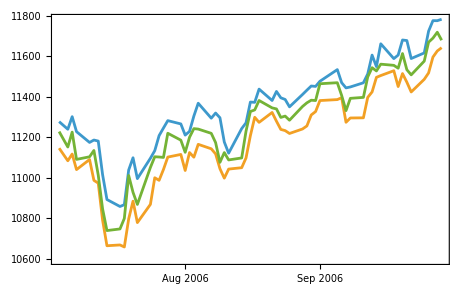

```mathematica
DateListPlot[td1,Ticks-> {dateTcks}]
```

## Gold or cryptocurrency?

```mathematica
(* Set a Time Period *)
startDate=DateObject[{2004,01,2}];
endDate =DateObject[{2020,09,4}];
period = {startDate,endDate};
```

```mathematica
(****** IMPORT DATA ******)
```

```mathematica
(* Import Asset Data: Gold, Bitcoin & Ethereum Prices in USD *)
goldData=FinancialData["XAU/USD",period];
btcData= FinancialData["BTC/USD", period];
ethData = FinancialData["ETH/USD",period];
```

```mathematica
(* Import Index Data: CBOE VIX & S&P 500 measures *)
sp500Data = FinancialData["^SPX",period];
```

Chicago Board Options Exchange® (CBOE®) introduced the CBOE Volatility Index®, VIX®. Since  recently, not  possible  to  direct  download  vix  data . So, you  will  find  the  data  in  the  folder  for  lecture  5.

```mathematica
(*vixPath = "https://datahub.io/core/finance-vix/r/vix-daily.csv";
vixData = Import[vixPath];*)
```

```mathematica
(****** Bellow to export the data ******)
```

Wolfram 14.2 has updated Import to interpret Date String to DataObject. The consequence is that it takes much more time to Import the data. But it speeds up post-import pre-processing.

To disable this do :

```mathematica
SetFileFormatProperties["CSV","DefaultImportElement"->"RawData"]
```

<|DefaultImportElement→RawData|>

But notice that Data may be imported as strings, instead of numbers

```mathematica
(*to enable do SetFileFormatProperties["CSV","DefaultImportElement"->"Data"]*)
```

```mathematica
SetFileFormatProperties["CSV","DefaultImportElement"->"Data"]
```

<|DefaultImportElement→Data|>

```mathematica
(*---*)
```

```mathematica
vixData=Import["/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec5/vix-daily_csv.csv"]
```

Tabular preserves the format !

```mathematica
Import["/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec5/vix-daily_csv.csv","Tabular"]
```

```mathematica
(* Display Original Source VIX Data *)
vixData //Normal //Dataset
```

Dataset[<>]

```mathematica
(****** CLEANING AND PREPARING DATA ******)
```

```mathematica
(* Prepare VIX Data *)
```

Let us eliminate key row :

```mathematica
vixData[[1,All]]
```

{Date,VIX Open,VIX High,VIX Low,VIX Close}

```mathematica
vixData=Drop[vixData,1]
```

```mathematica
Dimensions[vixData]
```

{4199,5}

```mathematica
vixData;
```

```mathematica
StringSplit["2004-01-02","-"]
```

{2004,01,02}

```mathematica
Head[%[[1]]]
```

String

```mathematica
Head[ToExpression["2004"]]
```

Integer

with elements in the list being Strings

To transform the strings to integers, use:

```mathematica
ToExpression[StringSplit["2004-01-02","-"]]
```

{2004,1,2}

```mathematica
(*------RuleDelayed----*)
```

Let us see the RuleDelayed function:

```mathematica
(* :> (type :>) *) : RuleDelayed
```

First the Rule :

```mathematica
{x,x,y,x}/. x-> RandomReal[]
```

{0.180567,0.180567,y,0.180567}

The right - hand side is evaluated separately each time it is used :

```mathematica
{x,x,x}/. x:>  RandomReal[]
```

{0.64691,0.875607,0.577371}

To enter RuleDelayed type :>

```mathematica
(*------------*)
```

The rule delayed here is necessary since without it the whole data will be transformed to a 2 columns dataset, but the replace all attempts to find a structure with 5 columns. Notice bellow the ToExpression to transform a string h into a number

```mathematica
vixData/.{d_,e_,f_,g_,h_} :>{DateObject[ToExpression@StringSplit[d,"-"]],ToExpression[h]}
```

```mathematica
vixDataClean=TimeSeries[vixData/.{d_,e_,f_,g_,h_}:> {DateObject[ToExpression@StringSplit[d,"-"]],ToExpression[h]}]
```

TimeSeries[…]

```mathematica
vixDataClean["Values"];
```

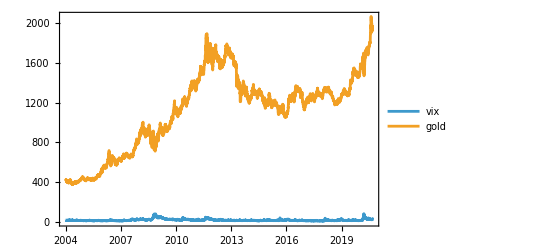

```mathematica
DateListPlot[{vixDataClean,goldData},PlotLegends->{"vix","gold"}]
```

```mathematica
|
```

The dates could be converted using a NEW function (v. 12.3):

```mathematica
FromDateString["2021-03-09",<|"Elements"->{"Year","Month","Day"},"Delimiters"->"-"|>]
```

Tue 9 Mar 2021

```mathematica
FromDateString["04/2022/09",<|"Elements"->{"Month","Year","Day"},"Delimiters"->"/"|>]
```

Sat 9 Apr 2022

```mathematica
vixDataClean1=TimeSeries[vixData/.{d_,e_,f_,g_,h_}:> {FromDateString[d,<|"Elements"->{"Year","Month","Day"},"Delimiters"->"-"|>],ToExpression[h]}]
```

TimeSeries[…]

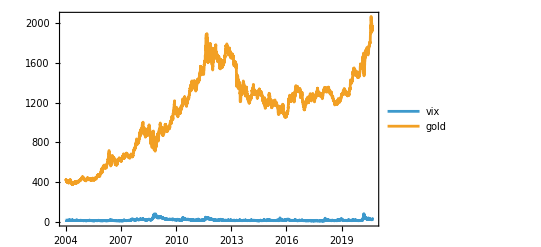

```mathematica
DateListPlot[{vixDataClean1,goldData},PlotLegends->{"vix","gold"}]
```

## Using Tabular

```mathematica
vixtabular=Import["/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025/DataDir/Lec5/vix-daily_csv.csv","Tabular"]
```

```mathematica
vixtabular[All,"VIX Close"]
```

TabularColumn[…]

To see 1 column use :

```mathematica
vixtabular[All,"VIX Close"]//Normal;
```

To see 2 or more use:

```mathematica
vixtabular[All,{"Date", "VIX Close"}];
```

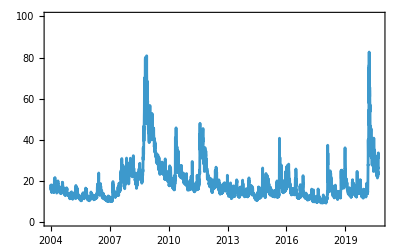

```mathematica
DateListPlot[vixtabular->{"Date","VIX Close"},PlotRange->{Automatic,{0,100}}]
```

# Sound

Sound and image can be trivially imported with Import. You will need to understand how to manipulate it

The Wolfram System treats sounds much like graphics. In fact, the Wolfram System allows you to combine graphics with sound to create pictures with “sound tracks”.

The sound objects have head Sound, and contain a list of sound primitives, which represent sounds to be played in sequence.

```mathematica
snd=Import["ExampleData/rule30.wav", "Sound"]
```

-Graphics-

Audio[…] displays an audio player.

```mathematica
Audio[snd]
```

# Represent a file in audio

An audio object linking to a local file :

```mathematica
File["ExampleData/car.mp3"]
```

File[ExampleData/car.mp3]

```mathematica
Audio[File["ExampleData/car.mp3"]]
```

# Record Sound

Use AudioCapture to record a sound interactively

```mathematica
hh=AudioCapture[]
```

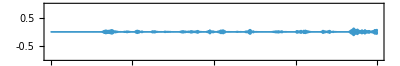

```mathematica
AudioPlot[hh]
```

```mathematica
AudioData[hh]
```

# Play audio from amplitudes given by argument

For example, just as you can use Plot[f, {x, xmin, xmax}] to plot a function, so also you can use Play[f, {t, 0, tmax}] to "play" a function. Play takes the function to define the waveform for a sound : the values of the function give the amplitude of the sound as a function of time.

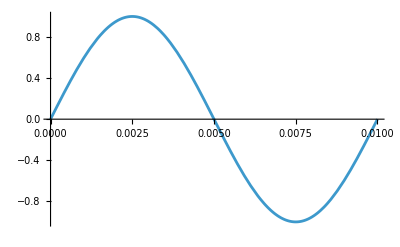

```mathematica
Plot[Sin[2Pi 100t],{t,0,0.01}]
```

```mathematica
Play[Sin[200 Pi t],{t,0,10}]
```

-Graphics-

# Processing Audio

A complete list of functions to process audion can be seen in documentation

I comment here on two : AudioData and SpeechSynthesize

```mathematica
hhh=AudioData[-Graphics-] // Shallow
```

{{0.156434,0.309017,0.45399,0.587785,0.707107,0.809017,0.891007,0.951057,0.987688,1.,«7990»}}

```mathematica
Flatten[hhh[[1]]]
```

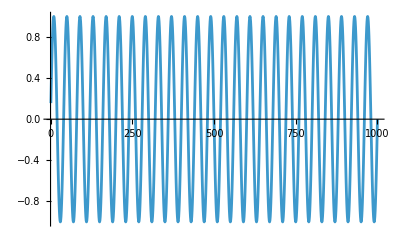

```mathematica
ListLinePlot[Flatten[hhh[[1]]][[;;1000]]]
```

Notice that the X coordinate is not the time, but the angle inside the argument of the Sin () function . 400 Pi is the angle representing a time interval of 1 s

#### If SpeechSynthesize produces internal error use : AudioPlay[SpeechSynthesize["Hello Wolfram"]]

```mathematica
SpeechSynthesize["Hello Wolfram"]
```

List of available voices :

```mathematica
VoiceStyleData[]//Dataset
```

```mathematica
$VoiceStyles;
```

```mathematica
voice=RandomChoice[VoiceStyleData[#Gender=="Female"&]]
```

<|Gender→Female,Language→Indonesian,LanguageCode→id-ID,Name→Damayanti|>

```mathematica
RandomChoice[VoiceStyleData[#Gender=="Female"&]]
```

<|Gender→Female,Language→Bangla,LanguageCode→bn-IN,Name→Piya|>

```mathematica
VoiceStyleData[#Language=="Portuguese"&]
```

{<|Gender→Missing[],Language→Portuguese,LanguageCode→pt_BR,Name→Cadu (Medium)|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt-BR,Name→Eddy (Portuguese - Brazil)|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt_BR,Name→Edresson (Low)|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt_BR,Name→Faber (Medium)|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt-BR,Name→Flo (Portuguese - Brazil)|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt-BR,Name→Grandma (Portuguese - Brazil)|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt-BR,Name→Grandpa (Portuguese - Brazil)|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt_BR,Name→Jeff (Medium)|>,<|Gender→Female,Language→Portuguese,LanguageCode→pt-PT,Name→Joana|>,<|Gender→Female,Language→Portuguese,LanguageCode→pt-BR,Name→Luciana|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt-BR,Name→Reed (Portuguese - Brazil)|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt-BR,Name→Rocko (Portuguese - Brazil)|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt-BR,Name→Sandy (Portuguese - Brazil)|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt-BR,Name→Shelley (Portuguese - Brazil)|>,<|Gender→Missing[],Language→Portuguese,LanguageCode→pt_PT,Name→Tugão (Medium)|>}

```mathematica
voice=First[VoiceStyleData[#Language=="Portuguese"&& #Gender== "Female"&]]
```

<|Gender→Female,Language→Portuguese,LanguageCode→pt-PT,Name→Joana|>

```mathematica
voice=First[VoiceStyleData[#Language=="Portuguese"&& #Name=="Shelley (Portuguese - Brazil)"&]]
```

<|Gender→Missing[],Language→Portuguese,LanguageCode→pt-BR,Name→Shelley (Portuguese - Brazil)|>

```mathematica
SpeechSynthesize["Olá seus Pirralhos bagunceiros!",voice]
```

```mathematica
SpeechSynthesize["Murilo, vocé é muito legal!","Luciana"]
```

```mathematica
SpeechSynthesize["Murilo, vocé é muito legal!","Luciana"]
```

```mathematica
voice_French=VoiceStyleData[#Language=="French"&];
```

```mathematica
SpeechSynthesize["Bonjour Clinton comment vas tu ?","Eddy (French - Canada)"]
```

# Images

Many functions in the Wolfram Language work on images. It’s easy to get an image into the Wolfram Language, for example by copying or dragging it from the web or from a photo collection.

You can also just capture an image directly from your camera using the function CurrentImage.

```mathematica
eu=CurrentImage[]
```

-Graphics-

```mathematica
IMAQ`StopCamera[]
```

If webcamera does not switch off use : 

  	IMAQ`StopCamera[]. 
  	
  	Similarly IMAQ`StartCamera[] will turn it back on again.
  	
    	Alternatively you can use the On/Off button on the control interface returned by ImageCapture[]

```mathematica
ImageCapture[]
```

We can also import an image from a file :

```mathematica
g=Import["ExampleData/ocelot.jpg"]
```

-Graphics-

## MatrixPlot

You can also use the function MatrixPLot[m] whose argument is a matrix whose values are plotted by colours in the respective image cells, and the palette of colours can be set using the option ColorFunction. The MatrixPLot is appropriate when plotting values obtained for example from a Correlation matrix to be discussed in our Lecture 8 (about Techniques).

If you then want to show the chosen palette of colours and how they relate to the coefficients you should use the function BarLegend. Take a look at the forum discussion in Link

```mathematica
corr=RandomReal[{-1,1},{5,5}];corr//MatrixForm
```

(0.16033 | 0.930102 | 0.532319 | -0.153393 | -0.148067
-0.0978272 | -0.569606 | -0.639999 | 0.859108 | -0.759566
-0.968073 | 0.605051 | 0.218624 | 0.727845 | -0.178917
-0.205617 | 0.0567566 | -0.198507 | 0.137313 | -0.48582
0.540404 | -0.838077 | -0.827949 | -0.252427 | -0.740491)

Suppose variables in X and Y to be :

```mathematica
Xlabel=Transpose[{Range[1,5],{"A1","A2","A3","A4","A5"}}];
Ylabel=Transpose[{Range[1,5],{"B1","B2","B3","B4","B5"}}];
```

```mathematica
MatrixPlot[corr,
ColorFunction->"ThermometerColors",PlotLegends->BarLegend[Automatic],
FrameTicks->{Ylabel,Xlabel},ImageSize->Large]
```

-Graphics-

Let us plot the Global-mean monthly, seasonal, and annual means, 1890-present, updated through most recent month, which can be downloaded from NASA: https://data.giss.nasa.gov/gistemp/

run command below :

```mathematica
(*SetFileFormatProperties["CSV","DefaultImportElement"->"RawData"]*)
```

In case you want to return to the standard:

```mathematica
(* SetFileFormatProperties["CSV","DefaultImportElement"->"Data"]*)
```

<|DefaultImportElement→Data|>

```mathematica
temp=Import["https://data.giss.nasa.gov/gistemp/tabledata_v4/GLB.Ts+dSST.csv"];
```

```mathematica
Dimensions[temp]
```

{147,19}

```mathematica
temp[[2,All]];
```

```mathematica
temp[[-3;;-1]]
```

{{2023,0.88,0.97,1.23,0.99,0.94,1.09,1.2,1.19,1.48,1.34,1.4,1.37,1.17,1.13,.88,1.05,1.16,1.41},{2024,1.25,1.44,1.39,1.31,1.15,1.2,1.2,1.29,1.24,1.33,1.3,1.27,1.28,1.29,1.36,1.28,1.23,1.29},{2025,1.38,1.26,1.36,1.23,1.08,1.05,1.02,1.16,1.25,1.19,1.21,1.05,1.19,1.21,1.30,1.22,1.08,1.22}}

To extract monthly data from 1890 until 2025, without the Keys attributes (year and months), and without first column (year)

```mathematica
temp1=temp[[12;;-1,2;;13]];
```

```mathematica
Dimensions[temp1]
```

{136,12}

```mathematica
temp1[[-1,2]]
```

1.26

```mathematica
temp1[[-1,2]]//Head
```

Real

```mathematica
listYears=Table[DateObject[ToString[i]],{i,1890,2025}];
```

```mathematica
temp[[1]];
```

```mathematica
listMonths=temp[[1,2;;13]]
```

{Jan,Feb,Mar,Apr,May,Jun,Jul,Aug,Sep,Oct,Nov,Dec}

```mathematica
Dimensions[listYears]
```

{136}

```mathematica
period=2025-1890+1
```

136

```mathematica
Range[1,period];
```

```mathematica
Xlabel=Transpose[{Range[1,12],listMonths}]
```

{{1,Jan},{2,Feb},{3,Mar},{4,Apr},{5,May},{6,Jun},{7,Jul},{8,Aug},{9,Sep},{10,Oct},{11,Nov},{12,Dec}}

```mathematica
Ylabel=Transpose[{Range[1,period],listYears}];
```

```mathematica
MatrixPlot[temp1];
```

ToExpression below is in case temp1 are Imported as strings, which is not the case, but inert if values in temp1 are Real

```mathematica
MatrixPlot[ToExpression[temp1],
ColorFunction->"ThermometerColors",PlotLegends->BarLegend[Automatic],FrameTicks->{Ylabel,Xlabel},ImageSize->Large]
```

-Graphics-

Notice how much the planet is getting hot !

More  reading  on  this  subject :

The Guardian: https://www.theguardian.com/environment/2024/feb/17/february-on-course-to-break-unprecedented-number-of-heat-records

Source data: https://climatereanalyzer.org/clim/sst_daily/

# Image

Create a grey-color image from a 3*3 array :

```mathematica
Image[({{0.1, 0.2, 0.3}, {0.4, 0.5, 0.6}, {0.7, 0.7, 0.9}})]
```

-Graphics-

Create an RGB channel image from a 3 D array :

```mathematica
Image[({{({{0}, {0.6}, {0}}), ({{0.4}, {0.1}, {0.8}}), ({{0.7}, {0.9}, {0.7}})}, {({{1}, {0}, {0.9}}), ({{0.6}, {0.6}, {1}}), ({{1}, {0.8}, {0.3}})}}), ColorSpace -> "RGB"]
```

-Graphics-

# Image Processing & Analysis

A list of commands can be seen in the documentation

I will comment on 2 commands : ImageData and Binarize

Channel data for the first five pixels of the first row :

```mathematica
ImageData[-Graphics-][[1, 1 ;; 5]]
```

{{0.866667,0.545098,0.258824},{0.85098,0.529412,0.25098},{0.847059,0.533333,0.262745},{0.858824,0.545098,0.27451},{0.854902,0.541176,0.262745}}

Convert a colour image to binary :

```mathematica
Binarize[-Graphics-]
```

-Graphics-

Discuss the relevance of this Binarize function to border detection